```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ww0m1 = Import["ww0m1_partonic.dat","List"];
ww01 = Import["ww01_partonic.dat","List"];
ww10 = Import["ww10_partonic.dat","List"];
wwm10 = Import["wwm10_partonic.dat","List"];
ww00 = Import["ww00_partonic.dat","List"];
```

```mathematica
ww11 = Import["ww11_partonic.dat","List"];
wwm1m1 = Import["wwm1m1_partonic.dat","List"];
ww1m1 = Import["ww1m1_partonic.dat","List"];
wwm11 = Import["wwm11_partonic.dat","List"];
sqrtsList=Table[350+25*i,{i,0,400}];
```

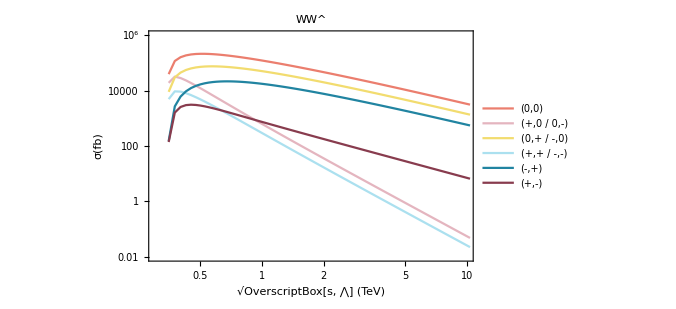

```mathematica
factor=0.3894*10^12;
lineplot=ListLogLogPlot[{Transpose[{sqrtsList/10^3,factor*ww00}],Transpose[{sqrtsList/10^3,factor*ww01}],Transpose[{sqrtsList/10^3,factor*ww10}],
Transpose[{sqrtsList/10^3,factor*ww11}],
Transpose[{sqrtsList/10^3,factor*ww1m1}],
Transpose[{sqrtsList/10^3,factor*wwm11}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9]},Frame->True,FrameLabel->{Style["\!\(\*SqrtBox[\(s^⋀\)]\) (TeV)",Black,17,FontFamily->"Times"],Style["σ(fb)",Black,18,FontFamily->"Times"]},
PlotLabel->Style["WW^"  ,Black,17,FontFamily->"Times"],
PlotLegends->{Placed[LineLegend[{Style[" (0,0) ",Black,15,FontFamily->"Times"],Style[" (+,0 / 0,-) ",Black,15,FontFamily->"Times"],Style[" (0,+ / -,0)",Black,15,FontFamily->"Times"],Style[" (+,+ / -,-) ",Black,15,FontFamily->"Times"],Style[" (-,+)",Black,15,FontFamily->"Times"],Style[" (+,-)",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",3}],{{0.15,0.14},{0.25,0.3}}]},
PlotRange->{{.300,10},{0.01,1000000}},FrameTicks->{{ticks1,Automatic},{{0.5,1,2,5,10},Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
(*customticks package*)
```

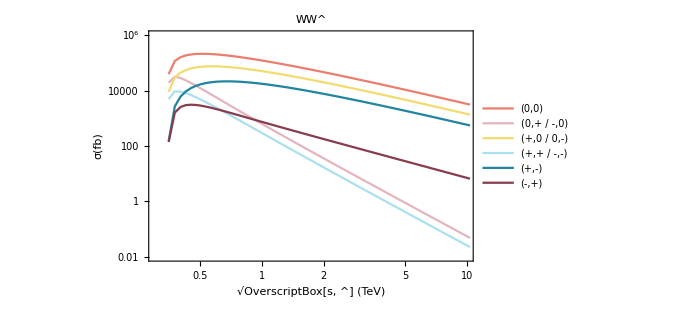

```mathematica
lineplot=ListLogLogPlot[{Transpose[{sqrtsList/10^3,factor*ww00}],Transpose[{sqrtsList/10^3,factor*ww01}],Transpose[{sqrtsList/10^3,factor*ww10}],
Transpose[{sqrtsList/10^3,factor*ww11}],
Transpose[{sqrtsList/10^3,factor*ww1m1}],
Transpose[{sqrtsList/10^3,factor*wwm11}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9]},Frame->True,FrameLabel->{Style["\!\(\*SqrtBox[\(ŝ\)]\) (TeV)",Black,16,FontFamily->"Times"],Style["σ(fb)",Black,16,FontFamily->"Times"]},
PlotLabel->Style["WW^"  ,Black,16,FontFamily->"Times"],
PlotLegends->{Style[" (0,0) ",Black,18,FontFamily->"Times"],Style[" (0,+ / -,0) ",Black,18,FontFamily->"Times"],Style[" (+,0 / 0,-)",Black,18,FontFamily->"Times"],Style[" (+,+ / -,-) ",Black,18,FontFamily->"Times"],Style[" (+,-)",Black,18,FontFamily->"Times"],Style[" (-,+)",Black,18,FontFamily->"Times"]},
PlotRange->{{.300,10},{0.01,1000000}},FrameTicks->{{ticks1,Automatic},{{0.5,1,2,5,10},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
ticks0=LogTicks[10,-2,6,TickLabelStep->2];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ishmammahbub/Desktop/Research/Partonic Distribution/WWtt/Plot Partonic Distribution

```mathematica
Export["WW_partonic.pdf",lineplot]
```

WW_partonic.pdf